```mathematica
(*Executive File to run the diferent numerical illustrations*)
SetDirectory[NotebookDirectory[]];
Import["PolynomialApproximationFunctions.m"]
```

```mathematica
(*Test1: Compound Poisson Distribution*)
(*Poisson distribution for the number of claims*)
NDist=PoissonDistribution[4];
(*Test 1: Gamma distribution for the claim sizes*)
UDist1=GammaDistribution[2,2];
(*Test 2: Uniform distribution for the claim sizes*)
UDist2=UniformDistribution[{0,8}];
(*We will study the survival function and the stop los premiums in each case, note that the these two compound distribution admit the same mean*)
(*Parameters for the polynomial approximation*)
r=1;
m1=16;
m2=16;
KPoly=75;
(*Parameters for Panjer's algorithm*)
h=1/100;uMax=32;(*uMax is equal to two times the mean*)
(*Parameters for the exponential Moment Technique*)
α=33;
b=1.115;
(*Parameters for the Direct Fourier Transform Inversion*)
a=18.5;
M=11;
KFourier=15;
```

```mathematica
(*Scor Color for the graphics*)
Graphics[{RGBColor[0,0.5,0.5],Disk[]}];
```

```mathematica
(*Computation of the coefficients of the polynomial expansion*)
N[CoeffsPolynomials1=CompoundDistributionPolynomialExpansionCoefficient[NDist,UDist1,r,m1,KPoly,False]]
N[CoeffsPolynomials2=CompoundDistributionPolynomialExpansionCoefficient[NDist,UDist2,r,m2,KPoly,False]]
(*PDF Approximation via Panjer algorithm*)
PDFPan1=PDFPanjer[NDist,UDist1,h,uMax];
PDFPan2=PDFPanjer[NDist,UDist2,h,uMax];
```

{0.981684,0.0183156,-0.330816,0.341232,-0.245855,0.136105,-0.0479601,-0.00990731,0.0407144,-0.0515935,0.0498169,-0.0412927,0.0302105,-0.0192054,0.00970617,-0.00230045,-0.00295446,0.00629557,-0.00809068,0.00873441,-0.008589,0.00795608,-0.00706841,0.00609329,-0.00514185,0.00428051,-0.00354235,0.00293717,-0.00245968,0.00209592,-0.00182781,0.00163633,-0.00150349,0.00141343,-0.00135294,0.00131152,-0.00128118,0.00125616,-0.00123253,0.00120782,-0.00118065,0.00115045,-0.0011172,0.00108122,-0.00104304,0.00100326,-0.000962504,0.000921341,-0.000880282,0.000839755,-0.000800101,0.000761579,-0.000724377,0.000688619,-0.000654375,0.000621674,-0.000590514,0.000560866,-0.000532686,0.000505918,-0.000480498,0.000456362,-0.000433442,0.000411672,-0.00039099,0.000371336,-0.000352653,0.000334888,-0.000317993,0.000301922,-0.000286632,0.000272085,-0.000258242,0.000245071,-0.000232539,0.000220616}

{0.981684,0.0183156,-0.351649,0.372482,-0.273177,0.150434,-0.0466549,-0.0248321,0.0648773,-0.0800892,0.078377,-0.0668339,0.0509432,-0.0344785,0.0197301,-0.00784324,-0.000839435,0.00648388,-0.00953612,0.0105585,-0.0101217,0.00874047,-0.00684205,0.004756,-0.0027183,0.000882993,0.000662697,-0.00188265,0.00277736,-0.0033714,0.00370343,-0.00381846,0.00376238,-0.00357832,0.0033044,-0.00297271,0.00260905,-0.00223323,0.00185966,-0.00149821,0.00115499,-0.000833268,0.00053415,-0.000257285,1.37911×10^-6,0.000235365,-0.000454929,0.000659249,-0.000850057,0.0010288,-0.00119659,0.00135419,-0.00150206,0.00164039,-0.0017691,0.00188795,-0.00199656,0.00209446,-0.00218114,0.00225608,-0.00231876,0.00236874,-0.00240562,0.0024291,-0.00243895,0.00243505,-0.00241738,0.002386,-0.00234108,0.00228288,-0.00221175,0.00212812,-0.00203251,0.00192548,-0.00180768,0.00167983}

```mathematica
(*Definition of the different aproximation of survival function*)
SurvivalPoly1=SurvivalCompoundDistributionPolynomial[NDist,UDist1,r,m1,KPoly,CoeffsPolynomials1];
SurvivalPoly2=SurvivalCompoundDistributionPolynomial[NDist,UDist2,r,m2,KPoly,CoeffsPolynomials2];
SurvivalPan1=SurvivalPanjer[PDFPan1,h];
SurvivalPan2=SurvivalPanjer[PDFPan2,h];
SurvivalExpMom1=SurvivalExponentialMomentsInterpolated[NDist,UDist1,α,b];
SurvivalExpMom2=SurvivalExponentialMomentsInterpolated[NDist,UDist2,α,b];
SurvivalFourier1=SurvivalInverseFourier[NDist,UDist1,a,KFourier,M];
SurvivalFourier2=SurvivalInverseFourier[NDist,UDist2,a,KFourier,M];
```

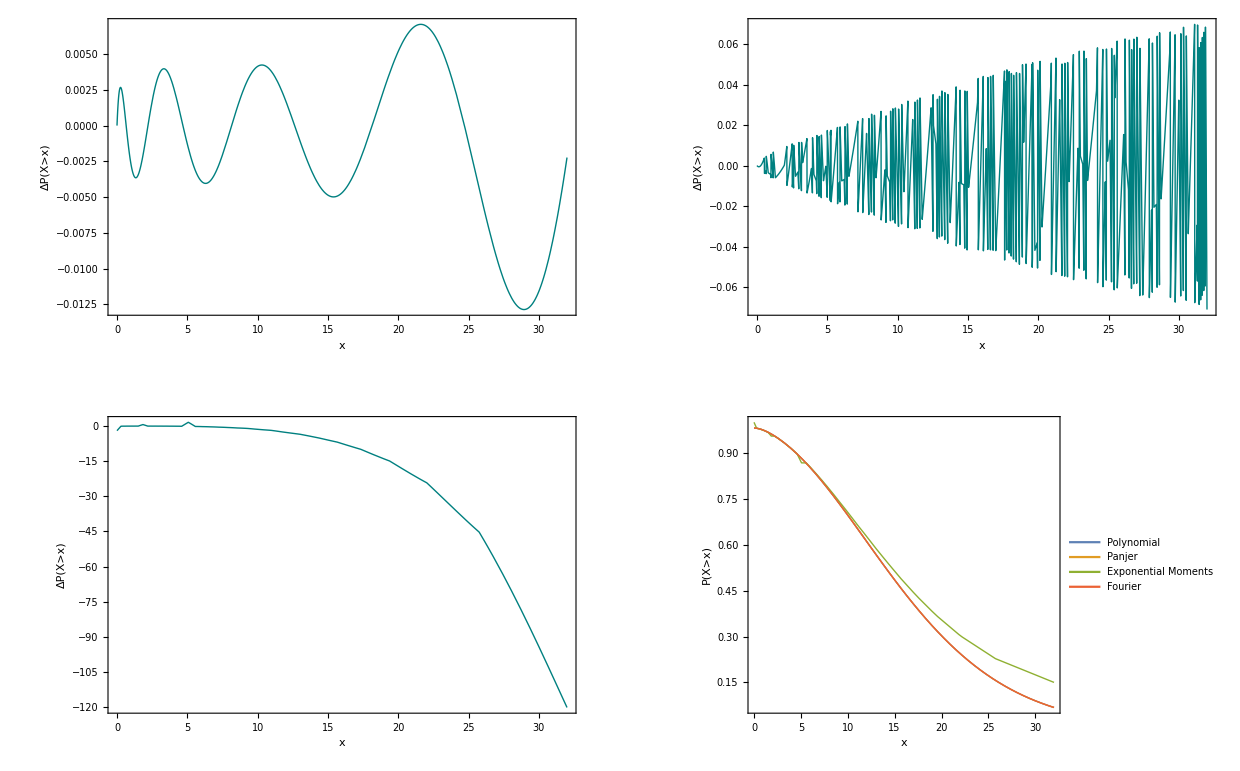

SurvivalErrorTest1ScorPaper.png

```mathematica
(*Graph of the relative error compared to the Fourier Transform Inversion technique and survival function for everybody*)
(*Test1*)
GraphicsGrid[{
{
Plot[(SurvivalFourier1[x]-SurvivalPoly1[x])/SurvivalFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}}],
Plot[(SurvivalFourier1[x]-SurvivalPan1[x])/SurvivalFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Panjer",24]}}]

},{Plot[(SurvivalFourier1[x]-SurvivalExpMom1[x])/SurvivalFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Exponential Moments",24]}}],
Plot[{SurvivalPoly1[x],SurvivalPan1[x],SurvivalExpMom1[x],SurvivalFourier1[x]},{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}}, 
PlotLegends->Placed[{Style["Polynomial",12],Style["Panjer",12],Style["Exponential Moments",12],Style["Fourier",12]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
}
}]
Export["SurvivalErrorTest1ScorPaper.png",%]
```

```mathematica
(*Table Survival Function Test 1*)
TeXForm[
Table[{N[x],N[SurvivalPoly1[x]],N[SurvivalFourier1[x]],N[SurvivalPan1[x]],N[SurvivalExpMom1[x]]},{x,uMax/10,uMax,uMax/10}]
]
```

\left(
\begin{array}{ccccc}
 3.2 & 0.934063 & 0.934099 & 0.93398 & 0.933795 \\
 6.4 & 0.838587 & 0.838553 & 0.838377 & 0.840413 \\
 9.6 & 0.713781 & 0.713808 & 0.713599 & 0.721811 \\
 12.8 & 0.577291 & 0.577288 & 0.577075 & 0.596213 \\
 16. & 0.445215 & 0.445194 & 0.444998 & 0.478344 \\
 19.2 & 0.328711 & 0.328722 & 0.328555 & 0.376255 \\
 22.4 & 0.233307 & 0.233322 & 0.23319 & 0.294725 \\
 25.6 & 0.159783 & 0.159777 & 0.159678 & 0.230831 \\
 28.8 & 0.105919 & 0.105905 & 0.105835 & 0.189891 \\
 32. & 0.0681425 & 0.068141 & 0.0680926 & 0.150105 \\
\end{array}
\right)

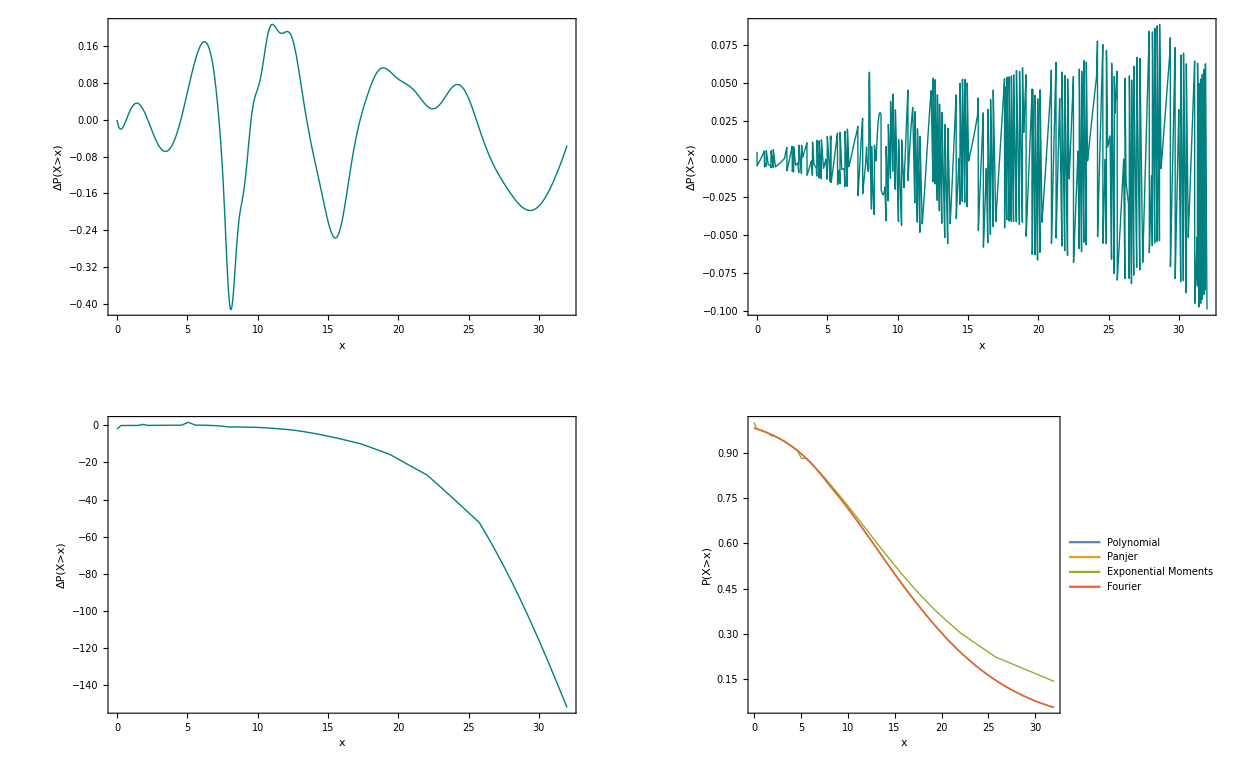

SurvivalErrorTest2ScorPaper.png

```mathematica
(*Graph of the relative error compared to the Fourier Transform Inversion technique and survival function for everybody*)
(*Test2*)
GraphicsGrid[{
{
Plot[(SurvivalFourier2[x]-SurvivalPoly2[x])/SurvivalFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}}],
Plot[(SurvivalFourier2[x]-SurvivalPan2[x])/SurvivalFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Panjer",24]}}]

},{Plot[(SurvivalFourier2[x]-SurvivalExpMom2[x])/SurvivalFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Exponential Moments",24]}}],
Plot[{SurvivalPoly2[x],SurvivalPan2[x],SurvivalExpMom2[x],SurvivalFourier2[x]},{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}}, 
PlotLegends->Placed[{Style["Polynomial",12],Style["Panjer",12],Style["Exponential Moments",12],Style["Fourier",12]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
}
}]
Export["SurvivalErrorTest2ScorPaper.png",%]
```

```mathematica
(*Table Survival Function Test 2*)
TeXForm[
Table[{N[x],N[SurvivalPoly2[x]],N[SurvivalFourier2[x]],N[SurvivalPan2[x]],N[SurvivalExpMom2[x]]},{x,uMax/10,uMax,uMax/10}]
]
```

\left(
\begin{array}{ccccc}
 3.2 & 0.938961 & 0.938351 & 0.938257 & 0.93827 \\
 6.4 & 0.854291 & 0.855714 & 0.855543 & 0.855596 \\
 9.6 & 0.732761 & 0.73288 & 0.732558 & 0.740374 \\
 12.8 & 0.595608 & 0.596393 & 0.596109 & 0.613427 \\
 16. & 0.457167 & 0.456162 & 0.456011 & 0.490425 \\
 19.2 & 0.33164 & 0.332007 & 0.331828 & 0.382171 \\
 22.4 & 0.228604 & 0.228659 & 0.228532 & 0.295308 \\
 25.6 & 0.150394 & 0.150388 & 0.150301 & 0.227499 \\
 28.8 & 0.0945545 & 0.0943759 & 0.0942929 & 0.184724 \\
 32. & 0.0568335 & 0.0568018 & 0.0567642 & 0.143209 \\
\end{array}
\right)

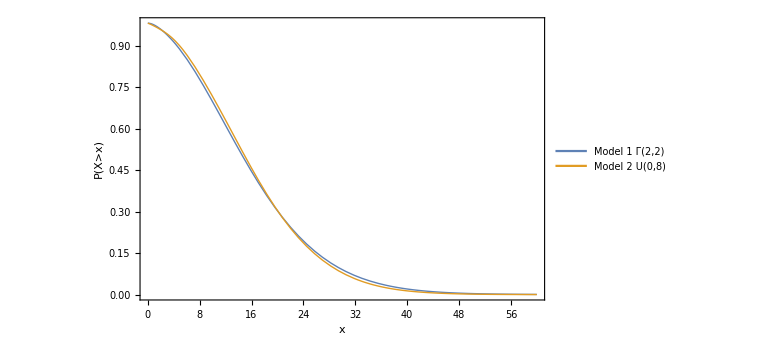

SurvivalTest1AndTest2ScorPaper.png

```mathematica
(*Survival Function for the two Test*)
Plot[{SurvivalPoly1[x],SurvivalPoly2[x]},{x,0,60},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}}, 
PlotLegends->Placed[{Style["Model 1 Γ(2,2)",16],Style["Model 2 U(0,8)",16]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
Export["SurvivalTest1AndTest2ScorPaper.png",%]
```

```mathematica
(*Stop Loss Premium Computation*)
(*Parameters for Monte Carlo confidence set*)
R=10000;(*Number of Replications*)
α=0.001; (*Confidence level*)
PracticalStopLossIC1=PracticalStopLossPremiumMonteCarloIC[NDist,UDist1,R,α];
PracticalStopLossIC2=PracticalStopLossPremiumMonteCarloIC[NDist,UDist2,R,α];
UsualStopLossIC1=UsualStopLossPremiumMonteCarloIC[NDist,UDist1,R,α];
UsualStopLossIC2=UsualStopLossPremiumMonteCarloIC[NDist,UDist2,R,α];
PracticalStopLossPoly1=PracticalStopLossPremiumCompoundDistributionPolynomial[NDist,UDist1,r,m1,KPoly,CoeffsPolynomials1];
PracticalStopLossPoly2=PracticalStopLossPremiumCompoundDistributionPolynomial[NDist,UDist2,r,m2,KPoly,CoeffsPolynomials2];
UsualStopLossPoly1=UsualStopLossPremiumCompoundDistributionPolynomial[NDist,UDist1,r,m1,KPoly,CoeffsPolynomials1];
UsualStopLossPoly2=UsualStopLossPremiumCompoundDistributionPolynomial[NDist,UDist2,r,m2,KPoly,CoeffsPolynomials2];
```

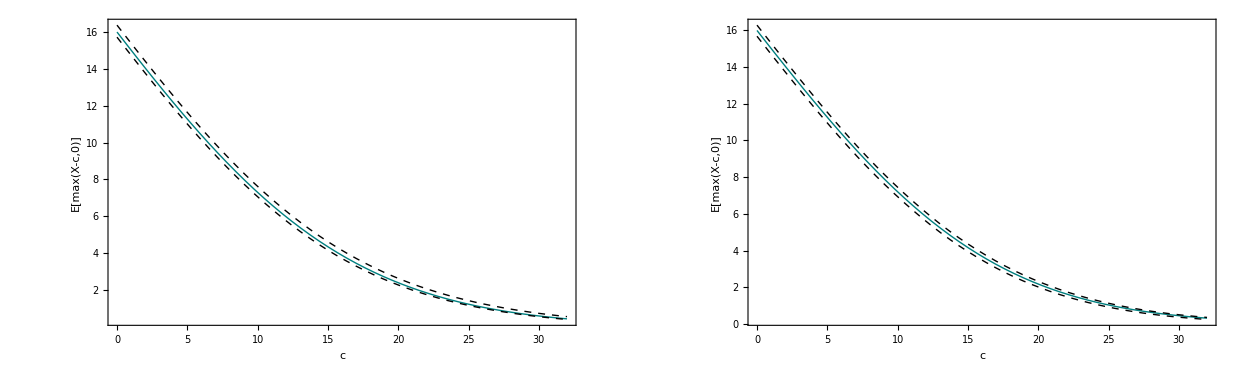

UsualStopLossPremiumTest1AndTest2ScorPaper.png

```mathematica
(*Usual Stop Loss Premium for the two Test*)
GraphicsGrid[{{
Plot[{UsualStopLossPoly1[c],UsualStopLossIC1[c][[1]],UsualStopLossIC1[c][[2]]},{c,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E[max(X-c,0)]",24],None},{Style["c",24],Style["Gamma Claim Sizes",24]}}],
Plot[{UsualStopLossPoly2[c],UsualStopLossIC2[c][[1]],UsualStopLossIC2[c][[2]]},{c,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E[max(X-c,0)]",24],None},{Style["c",24],Style["Uniform Claim Sizes",24]}}]}}]
Export["UsualStopLossPremiumTest1AndTest2ScorPaper.png",%]
```

```mathematica
(*3D Plots for the Practical Stop Loss Premium*)
GraphicsGrid[{
{Plot3D[PracticalStopLossPoly1[c,d],{c,0,32},{d,0,30},AxesLabel->Automatic,LabelStyle->Directive[Black,24],PlotStyle->RGBColor[0,0.5,0.5],ImageSize->Full,PlotLabel->"Gamma Claim Sizes"],
Plot3D[PracticalStopLossPoly1[c,d],{c,0,32},{d,0,30},AxesLabel->Automatic,LabelStyle->Directive[Black,24],PlotStyle->RGBColor[0,0.5,0.5],ImageSize->Full,PlotLabel->"Uniform Claim Sizes"]}}]
Export["PracticalStopLossPremiumTest1AndTest2ScorPaper3D.png",%]
```

-Graphics-

PracticalStopLossPremiumTest1AndTest2ScorPaper3D.png

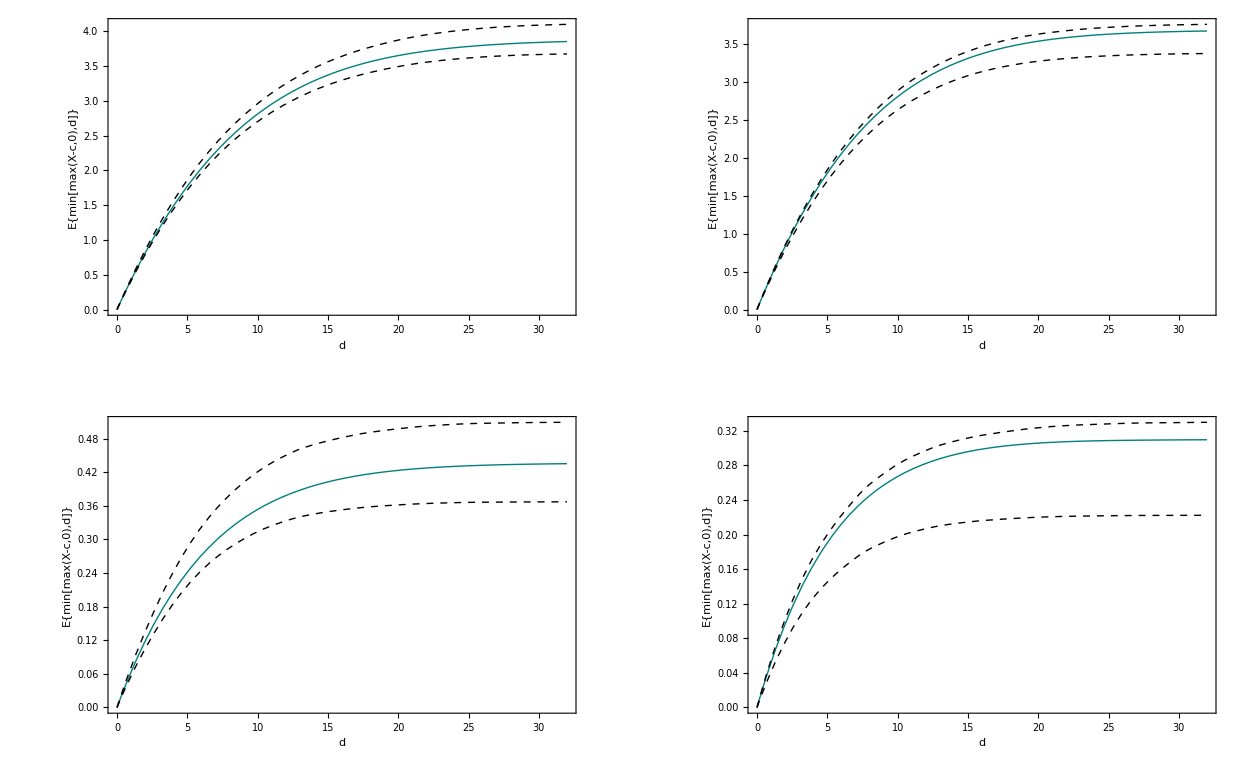

PracticalStopLossPremiumGivenRetentionLevelTest1AndTest2ScorPaper.png

```mathematica
(*Plots for the Practical Stop Loss Premium with a fixed rentention level*)
(*Usual Stop Loss Premium for the two Test*)
GraphicsGrid[{
{
Plot[{PracticalStopLossPoly1[16,d],PracticalStopLossIC1[16,d][[1]],PracticalStopLossIC1[16,d][[2]]},{d,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E{min[max(X-c,0),d]}",24],None},{Style["d",24],Style["Gamma Claim Sizes; c=16",24]}}],
Plot[{PracticalStopLossPoly2[16,d],PracticalStopLossIC2[16,d][[1]],PracticalStopLossIC2[16,d][[2]]},{d,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E{min[max(X-c,0),d]}",24],None},{Style["d",24],Style["Uniform Claim Sizes; c=16",24]}}]
},
{
Plot[{PracticalStopLossPoly1[32,d],PracticalStopLossIC1[32,d][[1]],PracticalStopLossIC1[32,d][[2]]},{d,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E{min[max(X-c,0),d]}",24],None},{Style["d",24],Style["Gamma Claim Sizes; c=32",24]}}],
Plot[{PracticalStopLossPoly2[32,d],PracticalStopLossIC2[32,d][[1]],PracticalStopLossIC2[32,d][[2]]},{d,0,32},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,
PlotStyle->{{Thick,RGBColor[0,0.5,0.5]},{Thick,Dashed,Black},{Thick,Dashed,Black}},LabelStyle->Directive[Black,24],
FrameLabel->{{Style["E{min[max(X-c,0),d]}",24],None},{Style["d",24],Style["Uniform Claim Sizes; c=32",24]}}]
}
}]
Export["PracticalStopLossPremiumGivenRetentionLevelTest1AndTest2ScorPaper.png",%]
```

```mathematica
(*Approximation of the ultimate ruin probability in the classical ruin model*)
(*Ruin model settings*)
(*Same Claim sizes distribution as in the study of the compound Poisson distribution*)
λ=4;(*Intensity of the Poisson Process*)
UDist1=GammaDistribution[2,2];
UDist2=UniformDistribution[{0,8}];
c=(1+0.2)*λ*Mean[UDist1];(*Safety loading of 20%*)
ρ=λ*Mean[UDist1]/c;(*Parameter of the geometric Distribution*)
NSolve[(MomentGeneratingFunction[UDist1,s]-1)/s/Mean[UDist1]==ρ^(-1),s,Reals]
NSolve[(MomentGeneratingFunction[UDist2,s]-1)/s/Mean[UDist2]==ρ^(-1),s,Reals]
```

0.833333

{{s→0.734975},{s→0.0566912}}

{{s→0.0654507}}

```mathematica
(*Parameters for the polynomial approximation*)
r=1;
m1=100/5;
m2=100/6;
KPoly=75;
(*Parameters for Panjer's algorithm*)
h=1/10;uMax=60;(*uMax is equal to two times the mean*)
(*Parameters for the exponential Moment Technique*)
α=32;
b=1.059;
(*Parameters for the Direct Fourier Transform Inversion*)
a=18.5;
M=11;
KFourier=15;
```

```mathematica
(*Computation of the coefficients of the polynomial expansion*)
N[CoeffsRuinProbaPolynomials1=RuinProbabilityPolynomialExpansionCoefficients[λ,c,UDist1,r,m1,KPoly,False,True]]
N[CoeffsRuinProbaPolynomials2=RuinProbabilityPolynomialExpansionCoefficients[λ,c,UDist2,r,m2,KPoly,False,True]]

(*PDF Approximation via Panjer algorithm*)
PDFRuinProbaPan1=PDFRuinProbabilityPanjer[λ,c,UDist1,h,uMax];
PDFRuinProbaPan2=PDFRuinProbabilityPanjer[λ,c,UDist2,h,uMax];
```

{0.833333,-0.0833333,-0.00416667,0.0135417,-0.0137604,0.0129589,-0.0120932,0.0112723,-0.0105057,0.00979103,-0.00912496,0.00850419,-0.00792566,0.00738648,-0.00688398,0.00641567,-0.00597921,0.00557245,-0.00519336,0.00484006,-0.00451079,0.00420392,-0.00391793,0.0036514,-0.00340299,0.00317149,-0.00295574,0.00275466,-0.00256726,0.00239261,-0.00222984,0.00207815,-0.00193677,0.00180502,-0.00168222,0.00156778,-0.00146112,0.00136173,-0.00126909,0.00118275,-0.00110229,0.0010273,-0.000957415,0.000892283,-0.000831581,0.000775009,-0.000722286,0.000673149,-0.000627355,0.000584676,-0.000544901,0.000507832,-0.000473284,0.000441087,-0.00041108,0.000383115,-0.000357051,0.000332761,-0.000310124,0.000289026,-0.000269364,0.000251039,-0.000233961,0.000218045,-0.000203211,0.000189387,-0.000176503,0.000164496,-0.000153305,0.000142876,-0.000133156,0.000124098,-0.000115655,0.000107787,-0.000100455,0.0000936207}

{0.833333,-0.0333333,-0.0306667,0.0334827,-0.0313118,0.0288331,-0.026435,0.0241485,-0.0219747,0.019912,-0.0179584,0.0161117,-0.0143698,0.0127301,-0.0111903,0.00974759,-0.00839942,0.00714296,-0.00597535,0.0048937,-0.00389503,0.00297636,-0.00213465,0.00136685,-0.000669888,0.0000407015,0.000523779,-0.00102661,0.00147084,-0.00185947,0.0021955,-0.00248187,0.0027215,-0.00291723,0.00307187,-0.00318818,0.00326884,-0.00331648,0.00333365,-0.00332283,0.00328643,-0.00322677,0.00314612,-0.00304664,0.00293042,-0.00279945,0.00265567,-0.00250089,0.00233686,-0.00216525,0.00198763,-0.00180547,0.00162018,-0.00143308,0.0012454,-0.00105829,0.000872805,-0.000689939,0.000510598,-0.000335613,0.000165737,-1.65315×10^-6,-0.000156029,0.000306768,-0.00045009,0.000585584,-0.000712901,0.000831755,-0.000941912,0.0010432,-0.00113548,0.0012187,-0.00129281,0.00135783,-0.00141382,0.00146088}

```mathematica
(*Determination of the different approximation*)
RuinProbaPoly1=RuinProbabilityPolynomialExpansion[λ,c,UDist1,r,m1,KPoly,CoeffsRuinProbaPolynomials1];
RuinProbaPoly2=RuinProbabilityPolynomialExpansion[λ,c,UDist2,r,m2,KPoly,CoeffsRuinProbaPolynomials2];
RuinProbaPan1=RuinProbabilityPanjer[PDFRuinProbaPan1,h];
RuinProbaPan2=RuinProbabilityPanjer[PDFRuinProbaPan2,h];
RuinProbaExpMom1=RuinProbabilityExponentialMoments[λ,c,UDist1,α,b];
RuinProbaExpMom2=RuinProbabilityExponentialMoments[λ,c,UDist2,α,b];
RuinProbaFourier1=RuinProbabilityInverseFourier[λ,c,UDist1,a,KFourier,M];
RuinProbaFourier2=RuinProbabilityInverseFourier[λ,c,UDist2,a,KFourier,M];
```

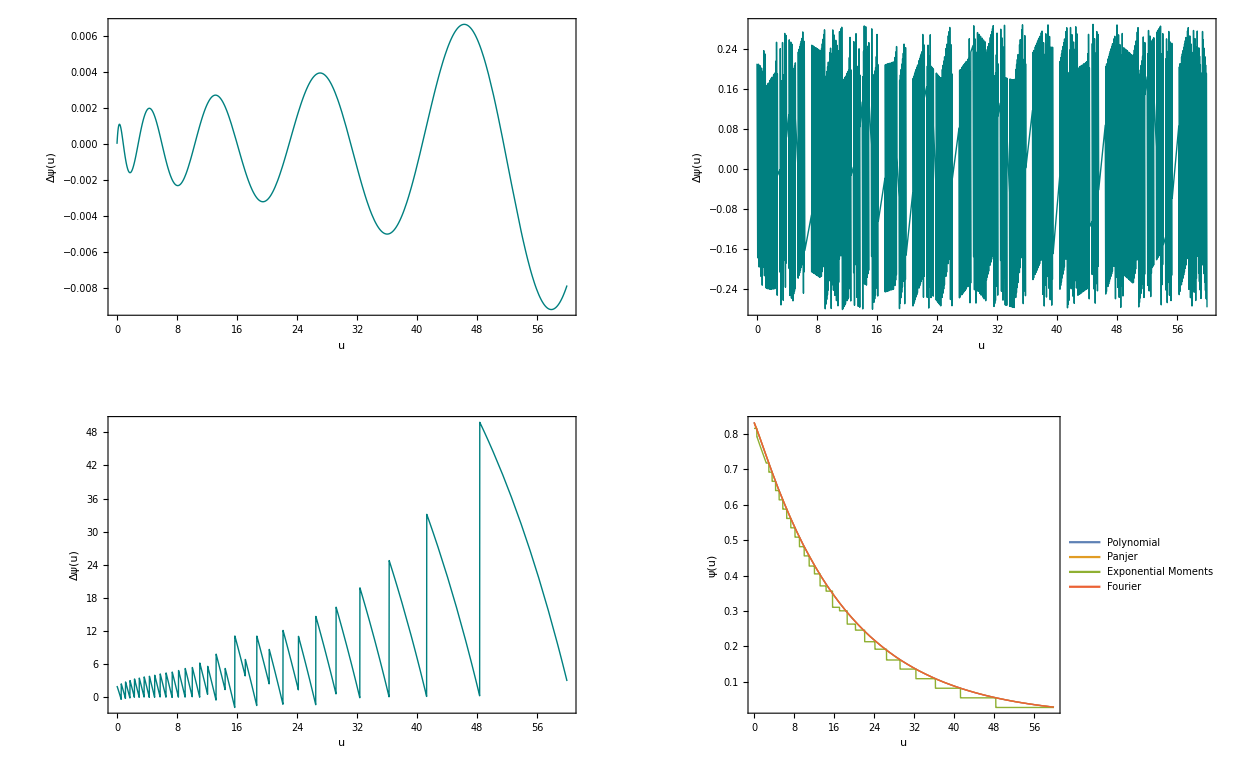

RuinProbaErrorModel1ScorPaper.png

```mathematica
(*Plot for the ultiate ruin probability for Model 1 and 2*)
(*Model1*)
GraphicsGrid[{
{
Plot[(RuinProbaFourier1[x]-RuinProbaPoly1[x])/RuinProbaFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Polynomial",24]}}],
Plot[(RuinProbaFourier1[x]-RuinProbaPan1[x])/RuinProbaFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Panjer",24]}}]

},{Plot[(RuinProbaFourier1[x]-RuinProbaExpMom1[x])/RuinProbaFourier1[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Exponential Moments",24]}}],
Plot[{RuinProbaPoly1[x],RuinProbaPan1[x],RuinProbaExpMom1[x],RuinProbaFourier1[x]},{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ψ(u)",24],None},{Style["u",24],Style["Ultimate Ruin Probability",24]}}, 
PlotLegends->Placed[{Style["Polynomial",12],Style["Panjer",12],Style["Exponential Moments",12],Style["Fourier",12]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
}
}]
Export["RuinProbaErrorModel1ScorPaper.png",%]
```

```mathematica
(*Table with the values of ultimate ruin probability in Model 1*)
TeXForm[
Table[{N[x],N[RuinProbaPoly1[x]],N[RuinProbaFourier1[x]],N[RuinProbaPan1[x]],N[RuinProbaExpMom1[x]]},{x,uMax/10,uMax,uMax/10}]
]
```

\left(
\begin{array}{ccccc}
 6. & 0.605967 & 0.605967 & 0.604246 & 0.587937 \\
 12. & 0.431393 & 0.431403 & 0.430169 & 0.427144 \\
 18. & 0.307024 & 0.307016 & 0.306137 & 0.300657 \\
 24. & 0.218489 & 0.218493 & 0.217865 & 0.213342 \\
 30. & 0.155491 & 0.155494 & 0.155046 & 0.136012 \\
 36. & 0.110665 & 0.11066 & 0.11034 & 0.108852 \\
 42. & 0.0787508 & 0.0787526 & 0.078525 & 0.0547796 \\
 48. & 0.0560422 & 0.0560455 & 0.0558832 & 0.0547796 \\
 54. & 0.0398876 & 0.0398856 & 0.0397699 & 0.0275445 \\
 60. & 0.0283874 & 0.0283852 & 0.0283027 & 0.0275445 \\
\end{array}
\right)

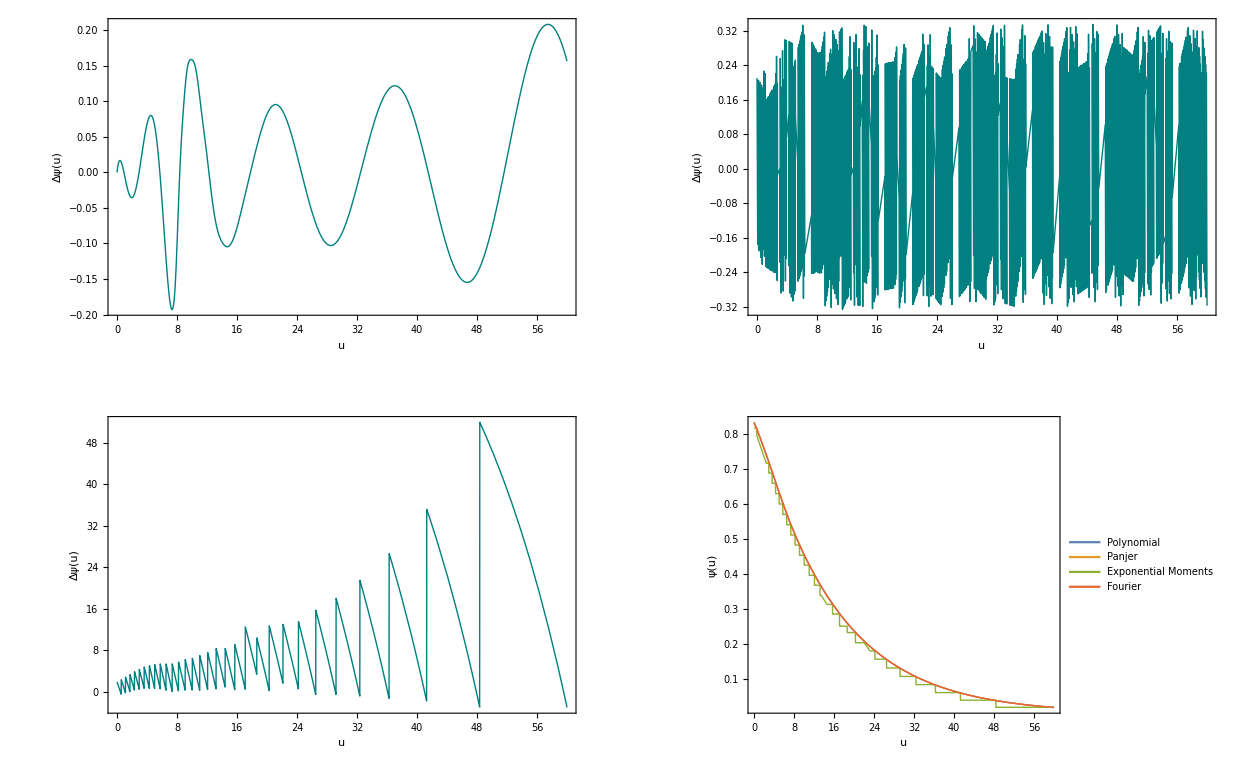

RuinProbaErrorModel2ScorPaper.png

```mathematica
(*Plot for the ultiate ruin probability for Model 1 and 2*)
(*Mode 2*)
GraphicsGrid[{
{
Plot[(RuinProbaFourier2[x]-RuinProbaPoly2[x])/RuinProbaFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Polynomial",24]}}],
Plot[(RuinProbaFourier2[x]-RuinProbaPan2[x])/RuinProbaFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Panjer",24]}}]

},{Plot[(RuinProbaFourier2[x]-RuinProbaExpMom2[x])/RuinProbaFourier2[x]*100,{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Directive[Thick,RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,24],
FrameLabel->{{Style["Δψ(u)",24],None},{Style["u",24],Style["Exponential Moments",24]}}],
Plot[{RuinProbaPoly2[x],RuinProbaPan2[x],RuinProbaExpMom2[x],RuinProbaFourier2[x]},{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ψ(u)",24],None},{Style["u",24],Style["Ultimate Ruin Probability",24]}}, 
PlotLegends->Placed[{Style["Polynomial",12],Style["Panjer",12],Style["Exponential Moments",12],Style["Fourier",12]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
}
}]
Export["RuinProbaErrorModel2ScorPaper.png",%]
```

```mathematica
(*Table with the values of ultimate ruin probability in Model 1*)
TeXForm[
Table[{N[x],N[RuinProbaPoly2[x]],N[RuinProbaFourier2[x]],N[RuinProbaPan2[x]],N[RuinProbaExpMom2[x]]},{x,uMax/10,uMax,uMax/10}]
]
```

\left(
\begin{array}{ccccc}
 6. & 0.592845 & 0.592607 & 0.590567 & 0.569688 \\
 12. & 0.399326 & 0.399418 & 0.398085 & 0.395597 \\
 18. & 0.269644 & 0.269669 & 0.268775 & 0.250033 \\
 24. & 0.182041 & 0.182086 & 0.181482 & 0.178938 \\
 30. & 0.123055 & 0.12295 & 0.122541 & 0.106104 \\
 36. & 0.0829246 & 0.0830192 & 0.0827425 & 0.0825649 \\
 42. & 0.0560697 & 0.056057 & 0.0558697 & 0.0380679 \\
 48. & 0.037905 & 0.0378513 & 0.0377245 & 0.0380679 \\
 54. & 0.0255273 & 0.0255583 & 0.0254725 & 0.0177739 \\
 60. & 0.0172307 & 0.0172577 & 0.0171996 & 0.0177739 \\
\end{array}
\right)

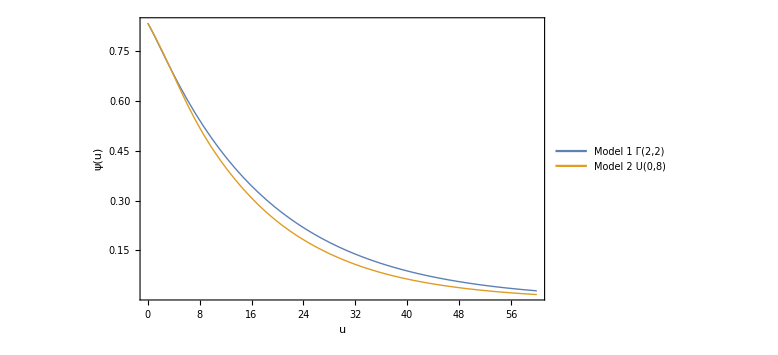

RuinProbaMoel1AndModel2ScorPaper.png

```mathematica
(*Comparison of the ruin probabilities in Model 1 and Model 2*)
Plot[{RuinProbaPoly1[x],RuinProbaPoly2[x]},{x,0,uMax},PlotRange->All,ImageSize->Large,Frame->True,Filling->None,PlotStyle->Thick,LabelStyle->Directive[Black,24],
FrameLabel->{{Style["ψ(u)",24],None},{Style["u",24],Style["Ultimate Ruin Probability",24]}}, 
PlotLegends->Placed[{Style["Model 1 Γ(2,2)",16],Style["Model 2 U(0,8)",16]}
,{Scaled[{0.65,0.9}], {0, 0.8}}]]
Export["RuinProbaMoel1AndModel2ScorPaper.png",%]
```